```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\critical_region\LPA\runningpoint\nu\phase\Tc\LPA_mub716p5\buffer

```mathematica
k=Flatten[Import["./k1.dat"]];
kappa=Flatten[Import["./kappa.dat"]];
lam1=Flatten[Import["./lam1.dat"]];
lam2=Flatten[Import["./lam2.dat"]];
rhobar=kappa[[1;;Length[k]]]/(k*57.08745);
lam1bar=lam1[[1;;Length[k]]]/k^2;
lam2bar=lam2[[1;;Length[k]]]/k;
```

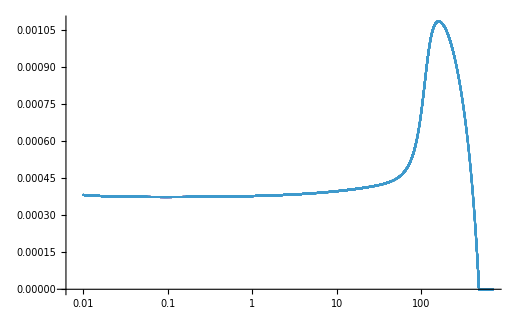

```mathematica
ListPlot[Transpose[{k*197.33,rhobar}],ScalingFunctions->{"Log",Automatic}]
```

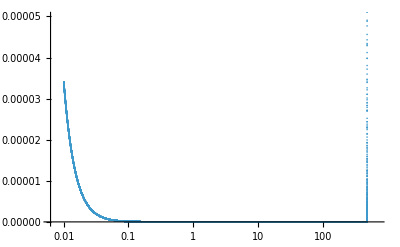

```mathematica
ListPlot[{Transpose[{k*197.33,lam1bar}]},ScalingFunctions->{"Log",Automatic},PlotRange->{All,{0,5 10^-5}}]
```

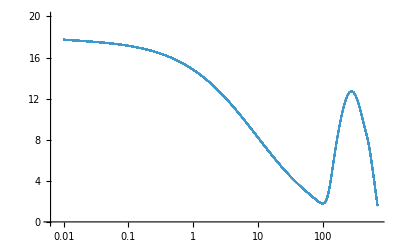

```mathematica
ListPlot[{Transpose[{k*197.33,lam2bar}]},ScalingFunctions->{"Log",Automatic},PlotRange->{All,{0,2 10^1}}]
```